#### Set-2 parameters

```mathematica
NSolve[{(b0/bz Sin[pz])^2+2Cos[pz](1+M0)-(1+(1+M0)^2-(bz^2-b0^2)/4)==0}/.bz->1.2/.b0->0.1/.M0->-0.3,{pz}]
BBLSet2={bz->1.2,b0->0.1,M0->-0.3,pzWR->pz/.%[[1]],ϵ0R->-0.1/1.2 Sin[pz]/.%[[1]],ϵ0L->+0.1/1.2 Sin[pz]/.%[[1]]}
Subscript[vSet2, perp]=Sqrt[4(bz^2-b0^2)/(bz^2-4 ϵ0R^2)]/.BBLSet2
Subscript[vSet2, parallel]=1/(2(bz^2-4 ϵ0R^2))Sqrt[2^2(4ϵ0R(1+M0)Sin[pzWR]+b0 bz Cos[pzWR])^2+4(bz^2-4 ϵ0R^2)(4(Sin[pzWR])^2(1+M0)^2-b0^2(Cos[pzWR])^2)]/.BBLSet2
vzcorrSet2=(-(4ϵ0R(1+M0)Sin[pzWR]+b0 bz Cos[pzWR]))/(bz^2-4 ϵ0R^2)/.BBLSet2
dPzMinSet2=ϵ0R/(Subscript[vSet2, parallel]-vzcorrSet2)/.BBLSet2
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{pz→-0.631403},{pz→0.-5.99541 ⅈ},{pz→0.+5.99541 ⅈ},{pz→0.631403}}

{bz→1.2,b0→0.1,M0→-0.3,pzWR→-0.631403,ϵ0R→0.0491898,ϵ0L→-0.0491898}

1.99978

0.687765

-0.0108816

0.0704073

```mathematica
lBSet2=50;
```

```mathematica
tRSet2=-Tan[1.49/2];
DispersionRSet2=Sqrt[2]tRSet2 Subscript[vSet2, perp]/lBSet2 ParabolicCylinderD[lBSet2^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2,Sqrt[2]py lBSet2]+(δϵ+Subscript[vSet2, parallel] dPz)ParabolicCylinderD[lBSet2^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2-1,Sqrt[2]py lBSet2]/.δϵ->ϵ-ϵ0R-vzcorrSet2 dPz/.BBLSet2;
dPzTrial=0;
(*Plot[DispersionRSet2/.py->-0.1/.dPz->dPzTrial,{ϵ,ϵ0R-Subscript[vSet2, parallel] dPzTrial+vzcorrSet2 dPzTrial-10^-6/.BBLSet2,ϵ0R-Subscript[vSet2, parallel] dPzTrial+vzcorrSet2 dPzTrial+10^-6/.BBLSet2}]*)
EnergyRSet2[pyVar_]:=ϵ/.FindRoot[DispersionRSet2/.py->pyVar/.dPz->dPzTrial,{ϵ,ϵ0R-Subscript[vSet2, parallel] dPzTrial+vzcorrSet2 dPzTrial/.BBLSet2}]
(*{EnergyRSet2[-0.1],ϵ0R-Subscript[vSet2, parallel] dPzTrial+vzcorrSet2 dPzTrial/.BBLSet2}*)
```

```mathematica
tRSet2mod=-Tan[-1./2];
DispersionRSet2modPhaseshift=Sqrt[2]tRSet2mod Subscript[vSet2, perp]/lBSet2 ParabolicCylinderD[lBSet2^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2,Sqrt[2]py lBSet2]+(δϵ+Subscript[vSet2, parallel] dPz)ParabolicCylinderD[lBSet2^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2-1,Sqrt[2]py lBSet2]/.δϵ->ϵ-ϵ0R-vzcorrSet2 dPz-vzQuadraticCorrectionSet2 dPz^3/.BBLSet2;
EnergyRSet2modPhaseshift[pyVar_]:=ϵ/.FindRoot[DispersionRSet2modPhaseshift/.py->pyVar/.dPz->dPzTrial,{ϵ,ϵ0R-Subscript[vSet2, parallel] dPzTrial+vzcorrSet2 dPzTrial/.BBLSet2}]
tRSet2mod2=-Tan[-2.3/2];
DispersionRSet2modPhaseshift2=Sqrt[2]tRSet2mod2 Subscript[vSet2, perp]/lBSet2 ParabolicCylinderD[lBSet2^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2,Sqrt[2]py lBSet2]+(δϵ+Subscript[vSet2, parallel] dPz)ParabolicCylinderD[lBSet2^2/Subscript[vSet2, perp]^2(δϵ^2-Subscript[vSet2, parallel]^2 dPz^2)/2-1,Sqrt[2]py lBSet2]/.δϵ->ϵ-ϵ0R-vzcorrSet2 dPz-vzQuadraticCorrectionSet2 dPz^3/.BBLSet2;
EnergyRSet2modPhaseshift2[pyVar_]:=ϵ/.FindRoot[DispersionRSet2modPhaseshift2/.py->pyVar/.dPz->dPzTrial,{ϵ,ϵ0R-Subscript[vSet2, parallel] dPzTrial+vzcorrSet2 dPzTrial/.BBLSet2}]
```

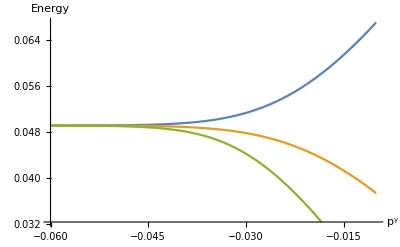

```mathematica
Plot[{EnergyRSet2[py],EnergyRSet2modPhaseshift[py],EnergyRSet2modPhaseshift2[py]},{py,-0.06,-0.01},AxesLabel->{p^y,Energy}]
Export["~/Downloads/boundary-states-dispersion.eps",%];
```